# Higgs to diphoton SM - attempt 1 with the FeynArts pipeline

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

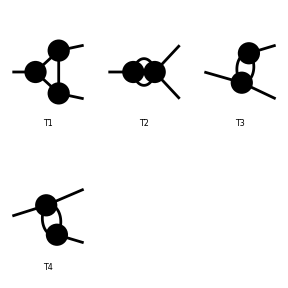

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSMQCD.mod

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 98 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 403 vertices

classes model {MSSMQCD} initialized

Excluding 0 Generic, 14 Classes, and 55 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 22 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

Restoring 0 Generic, 14 Classes, and 55 Particles fields

Restoring 18 field point(s)

in total: 28 Particles insertions

> Top. 1 ad/becf/dedfef.m, 22 diagrams

> Top. 2 ad/bece/dede.m, 2 diagrams

> Top. 3 ad/becd/eded.m, 2 diagrams

> Top. 4 ad/bdce/eded.m, 2 diagrams

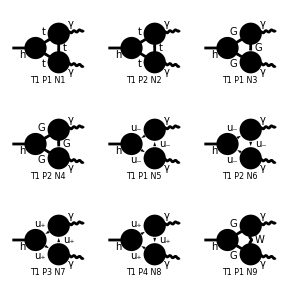

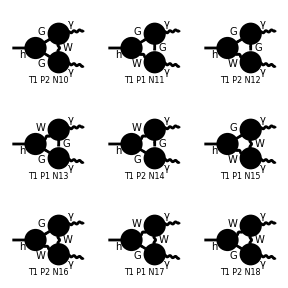

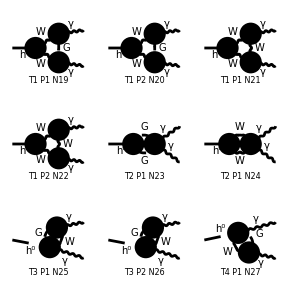

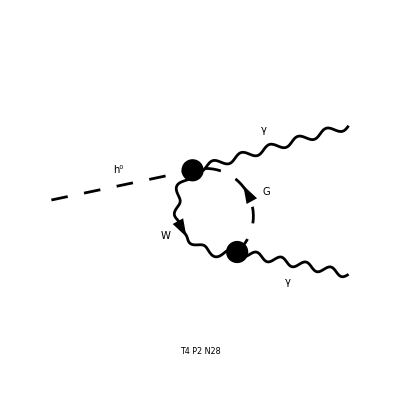

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[1],V[1]},InsertionLevel->{Particles},Model->"MSSMQCD",
ExcludeParticles->{(*V[1],V[2],V[3],V[4],*)S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[13,{2,3}],S[13,{1,3}],S[14],S[3],(*S[4],*)S[5],(*S[6],*)F[11],F[12](*,F[3],U[1],U[2],U[3],U[4]*)},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[(*OffShell[*)CreateFeynAmp[diag1](*,2-> mg1,3-> mg2]*),FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 22 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 28 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][1/(12 MW π SB SW)Alfa EL (16 CA MT2 Pair1 B0i[bb0,0,MT2,MT2]-3 MW2 Pair1 SB Sub1 B0i[bb0,Mh02,MW2,MW2]-8 Abb3 CA MT2 C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+3 MW2 SB Sub3 C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-64 CA MT2 Pair1 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+12 MW2 Pair1 SB Sub1 C0i[cc00,0,0,Mh02,MW2,MW2,MW2]+3 Mh02 MW2 Pair1 SB SBA C0i[cc1,0,0,Mh02,MW2,MW2,MW2]-64 CA MT2 Pair2 Pair3 C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+12 MW2 Pair2 Pair3 SB Sub1 C0i[cc12,0,0,Mh02,MW2,MW2,MW2]-16 Abb4 CA MT2 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+6 MW2 SB Sub2 C0i[cc2,0,0,Mh02,MW2,MW2,MW2]-64 CA MT2 Pair2 Pair3 C0i[cc22,0,0,Mh02,MT2,MT2,MT2]+12 MW2 Pair2 Pair3 SB Sub1 C0i[cc22,0,0,Mh02,MW2,MW2,MW2])]

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[expr]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][0]

0

#### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

mat= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-5.frm

running FORM...

ok

Note: polarization sum auto squares the matrix element. Subexpr seems to destroy this line.

```mathematica
(*mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify*)
```

# Input point

## Inputs

```mathematica
stopM1 = 250;
stopM2 = 10000;
mixT = 0;
muM = 250;
betaA = 1.47; (*tan beta = 10*)
alphaA = betaA - (Pi/2);
offM1 =0.0001;
offM2 = 0.0001;
Clear[matSq,c1,c2,ghSS,h11,h12,h22,z11,z12,z22,m,mh,mZ,mW]
```

# FeynArts Evaluation

## Numerical Evaluation

```mathematica
matPostSub = mat//.Subexpr[]//. mg1 -> offM1 //.mg2-> offM2
```

1/(18 π SB2 SW2)Alfa Alfa2 (-16 (-(16 CA2 MT2^2 (B0i[bb0,0,MT2,MT2]-4 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]))/MW2-3 CA MT2 SB (((C2B SAB)/CW2-6 SBA) B0i[bb0,Mh02,MW2,MW2]+((C2B MW2 SAB)/CW2+2 Mh02 SBA) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-4 ((C2B SAB)/CW2-6 SBA) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]+Mh02 SBA C0i[cc1,0,0,Mh02,MW2,MW2,MW2])+2 Mh02 ((8 CA2 MT2^2 (C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+2 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2])))/MW2+3 CA MT2 SB (((C2B SAB)/CW2-7 SBA) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])))) B0i[bb0,0,MT2,MT2]^*+3 (16 CA MT2 SB (((C2B SAB)/CW2-6 SBA) B0i[bb0,0,MT2,MT2]-4 ((C2B SAB)/CW2-6 SBA) C0i[cc00,0,0,Mh02,MT2,MT2,MT2])+3 SB2 (((C2B^2 MW2^2 SAB^2)/CW2^2+(2 C2B (Mh02 MW2-3 MW2^2) SAB SBA)/CW2-12 Mh02 MW2 SBA2) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]+MW2 (((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) B0i[bb0,Mh02,MW2,MW2]-4 ((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]+Mh02 ((C2B SAB SBA)/CW2-6 SBA2) C0i[cc1,0,0,Mh02,MW2,MW2,MW2]))-2 Mh02 (8 CA MT2 SB (((C2B SAB)/CW2-6 SBA) C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+2 ((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))+3 MW2 SB2 (((C2B^2 SAB^2)/CW2^2-(13 C2B SAB SBA)/CW2+42 SBA2) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])))) B0i[bb0,Mh02,MW2,MW2]^*+16 Mh02^2 (1/MW2 4 CA2 MT2^2 (C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+4 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))-3 CA MT2 SB (4 SBA C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2]))) C0i[cc0,0,0,Mh02,MT2,MT2,MT2]^*-3 (16 CA MT2 SB (-((C2B MW2 SAB)/CW2+2 Mh02 SBA) B0i[bb0,0,MT2,MT2]+4 Mh02^2 SBA C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+4 ((C2B MW2 SAB)/CW2+2 Mh02 SBA) C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+((C2B Mh02 MW2 SAB)/CW2+18 Mh02^2 SBA) C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+2 ((C2B Mh02 MW2 SAB)/CW2+10 Mh02^2 SBA) (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))-3 SB2 (((C2B^2 MW2^2 SAB^2)/CW2^2+(2 C2B (Mh02 MW2-3 MW2^2) SAB SBA)/CW2-12 Mh02 MW2 SBA2) B0i[bb0,Mh02,MW2,MW2]+((C2B^2 MW2^3 SAB^2)/CW2^2+(4 C2B Mh02 MW2^2 SAB SBA)/CW2+68 Mh02^2 MW2 SBA2) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-4 ((C2B^2 MW2^2 SAB^2)/CW2^2+(2 C2B (Mh02 MW2-3 MW2^2) SAB SBA)/CW2-12 Mh02 MW2 SBA2) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]+((C2B Mh02 MW2^2 SAB SBA)/CW2+2 Mh02^2 MW2 SBA2) C0i[cc1,0,0,Mh02,MW2,MW2,MW2]-2 ((C2B^2 Mh02 MW2^2 SAB^2)/CW2^2+(C2B (10 Mh02^2 MW2-7 Mh02 MW2^2) SAB SBA)/CW2-62 Mh02^2 MW2 SBA2) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]-2 ((C2B^2 Mh02 MW2^2 SAB^2)/CW2^2+(2 C2B (5 Mh02^2 MW2-3 Mh02 MW2^2) SAB SBA)/CW2-60 Mh02^2 MW2 SBA2) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2]))) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]^*+64 (-(16 CA2 MT2^2 (B0i[bb0,0,MT2,MT2]-4 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]))/MW2-3 CA MT2 SB (((C2B SAB)/CW2-6 SBA) B0i[bb0,Mh02,MW2,MW2]+((C2B MW2 SAB)/CW2+2 Mh02 SBA) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-4 ((C2B SAB)/CW2-6 SBA) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]+Mh02 SBA C0i[cc1,0,0,Mh02,MW2,MW2,MW2])+2 Mh02 ((8 CA2 MT2^2 (C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+2 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2])))/MW2+3 CA MT2 SB (((C2B SAB)/CW2-7 SBA) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])))) C0i[cc00,0,0,Mh02,MT2,MT2,MT2]^*-12 (16 CA MT2 SB (((C2B SAB)/CW2-6 SBA) B0i[bb0,0,MT2,MT2]-4 ((C2B SAB)/CW2-6 SBA) C0i[cc00,0,0,Mh02,MT2,MT2,MT2])+3 SB2 (((C2B^2 MW2^2 SAB^2)/CW2^2+(2 C2B (Mh02 MW2-3 MW2^2) SAB SBA)/CW2-12 Mh02 MW2 SBA2) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]+MW2 (((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) B0i[bb0,Mh02,MW2,MW2]-4 ((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]+Mh02 ((C2B SAB SBA)/CW2-6 SBA2) C0i[cc1,0,0,Mh02,MW2,MW2,MW2]))) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]^*+3 (-4 Mh02 (-18 MW2 SB2 SBA2 C0i[cc00,0,0,Mh02,MW2,MW2,MW2]+SBA (16 CA MT2 SB C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+(3 C2B MW2 SAB SB2 C0i[cc00,0,0,Mh02,MW2,MW2,MW2])/CW2))+Mh02^2 (3 MW2 SB2 SBA2 (2 C0i[cc0,0,0,Mh02,MW2,MW2,MW2]+C0i[cc1,0,0,Mh02,MW2,MW2,MW2]+14 C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+12 (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2]))-2 SBA (8 CA MT2 SB (C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+2 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))+(3 C2B MW2 SAB SB2 (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2]))/CW2))) C0i[cc1,0,0,Mh02,MW2,MW2,MW2]^*+3 Mh02 (8 (8 CA MT2 SB (((C2B SAB)/CW2-6 SBA) C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+2 ((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))+3 MW2 SB2 (((C2B^2 SAB^2)/CW2^2-(13 C2B SAB SBA)/CW2+42 SBA2) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2]))) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]^*+(SBA (16 CA MT2 SB B0i[bb0,0,MT2,MT2]+(3 C2B MW2 SAB SB2 B0i[bb0,Mh02,MW2,MW2])/CW2)+3 SB2 (-6 MW2 SBA2 B0i[bb0,Mh02,MW2,MW2]+(C2B MW2^2 SAB SBA C0i[cc0,0,0,Mh02,MW2,MW2,MW2])/CW2)) C0i[cc1,0,0,Mh02,MW2,MW2,MW2]^*)+16 (-3 CA MT2 SB ((C2B Mh02 MW2 SAB)/CW2+18 Mh02^2 SBA) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-Mh02 ((16 CA2 MT2^2 (B0i[bb0,0,MT2,MT2]-4 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]))/MW2+3 CA MT2 SB (((C2B SAB)/CW2-6 SBA) B0i[bb0,Mh02,MW2,MW2]-4 ((C2B SAB)/CW2-6 SBA) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]))+Mh02^2 (1/MW2 16 CA2 MT2^2 (C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+5 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+6 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))-3 CA MT2 SB (SBA C0i[cc1,0,0,Mh02,MW2,MW2,MW2]-2 ((3 C2B SAB)/CW2-19 SBA) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]-6 ((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])))) C0i[cc2,0,0,Mh02,MT2,MT2,MT2]^*+6 (-3 SB2 ((C2B^2 Mh02 MW2^2 SAB^2)/CW2^2+(C2B (10 Mh02^2 MW2-7 Mh02 MW2^2) SAB SBA)/CW2-62 Mh02^2 MW2 SBA2) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-Mh02 (16 CA MT2 SB (((C2B SAB)/CW2-7 SBA) B0i[bb0,0,MT2,MT2]-4 ((C2B SAB)/CW2-7 SBA) C0i[cc00,0,0,Mh02,MT2,MT2,MT2])+3 MW2 SB2 (((C2B^2 SAB^2)/CW2^2-(13 C2B SAB SBA)/CW2+42 SBA2) B0i[bb0,Mh02,MW2,MW2]-4 ((C2B^2 SAB^2)/CW2^2-(13 C2B SAB SBA)/CW2+42 SBA2) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]))+Mh02^2 (8 CA MT2 SB (((C2B SAB)/CW2-6 SBA) C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+2 ((3 C2B SAB)/CW2-19 SBA) C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+4 ((2 C2B SAB)/CW2-13 SBA) (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))-3 MW2 SB2 (((C2B SAB SBA)/CW2-7 SBA2) C0i[cc1,0,0,Mh02,MW2,MW2,MW2]-2 ((2 C2B^2 SAB^2)/CW2^2-(26 C2B SAB SBA)/CW2+85 SBA2) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]-2 ((2 C2B^2 SAB^2)/CW2^2-(25 C2B SAB SBA)/CW2+78 SBA2) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])))) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]^*+32 (-3 CA MT2 SB ((C2B Mh02 MW2 SAB)/CW2+10 Mh02^2 SBA) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-Mh02 ((16 CA2 MT2^2 (B0i[bb0,0,MT2,MT2]-4 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]))/MW2+3 CA MT2 SB (((C2B SAB)/CW2-6 SBA) B0i[bb0,Mh02,MW2,MW2]-4 ((C2B SAB)/CW2-6 SBA) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]))+Mh02^2 (1/MW2 8 CA2 MT2^2 (C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+6 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+8 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))-3 CA MT2 SB (SBA C0i[cc1,0,0,Mh02,MW2,MW2,MW2]-2 ((2 C2B SAB)/CW2-13 SBA) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]-4 ((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])))) (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]^*+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]^*)+6 (-3 SB2 ((C2B^2 Mh02 MW2^2 SAB^2)/CW2^2+(2 C2B (5 Mh02^2 MW2-3 Mh02 MW2^2) SAB SBA)/CW2-60 Mh02^2 MW2 SBA2) C0i[cc0,0,0,Mh02,MW2,MW2,MW2]-Mh02 (16 CA MT2 SB (((C2B SAB)/CW2-6 SBA) B0i[bb0,0,MT2,MT2]-4 ((C2B SAB)/CW2-6 SBA) C0i[cc00,0,0,Mh02,MT2,MT2,MT2])+3 MW2 SB2 (((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) B0i[bb0,Mh02,MW2,MW2]-4 ((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) C0i[cc00,0,0,Mh02,MW2,MW2,MW2]))+Mh02^2 (8 CA MT2 SB (((C2B SAB)/CW2-6 SBA) C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+6 ((C2B SAB)/CW2-6 SBA) C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+8 ((C2B SAB)/CW2-6 SBA) (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))+3 MW2 SB2 (-((C2B SAB SBA)/CW2-6 SBA2) C0i[cc1,0,0,Mh02,MW2,MW2,MW2]+2 ((2 C2B^2 SAB^2)/CW2^2-(25 C2B SAB SBA)/CW2+78 SBA2) C0i[cc2,0,0,Mh02,MW2,MW2,MW2]+4 ((C2B^2 SAB^2)/CW2^2-(12 C2B SAB SBA)/CW2+36 SBA2) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])))) (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]^*+C0i[cc22,0,0,Mh02,MW2,MW2,MW2]^*))

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
Alfas->0.12,Alfas2->(0.12)^2,
SW2->0.2228,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,MUEC-> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],CA2-> Cos[α]^2,
SBA->Sin[β-α],C2B-> Cos[2*β],SBA2-> Sin[β-α]^2,
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),AfC[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat],USf[2,1,3,3]-> -Sin[thetat],USf[2,2,3,3]-> Cos[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=matPostSub//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

```mathematica
feynArtsResult =Chop[MyMatrixElement[stopM1,stopM2,mixT,muM,alphaA,betaA]]
```

0.149758

Partial decay width:

```mathematica
MyDecayRate[higgs_]:=1/(32π higgs)feynArtsResult
```

```mathematica
diphotonSMResults = MyDecayRate[125]
```

0.0000119174

## Compare with Carena Results

```mathematica
carenaAmp = (-8.32 + 1.84)
```

-6.48

```mathematica
carenaDW = (fc*α^2*mh^3/(128*Sqrt[2]*Pi^3))*carenaAmp^2
```

0.00748127 fc mh^3 α^2

```mathematica
0.0074812716779899405 fc mh^3 α^2
```

0.00748127 fc mh^3 α^2

```mathematica
carenaDW = carenaDW /.mh-> 125/.α-> (1/128)/.fc-> 1.166379*10^(-5)
```

0.0000104022

```mathematica
carenaDW/diphotonSMResults
```

0.872859